```mathematica
res=Fit[{{20,0.013}, {30,0.0142}, {45,0.023}, {60,0.384}, {90,1.18}, {120,1.77}, {135,2.06}, {150,2.35}, {170,2.75}, {180,3.0051}},{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]
```

-4.20146+0.576209 x-0.0303426 x^2+0.000803682 x^3-0.0000118802 x^4+1.03454×10^-7 x^5-5.28161×10^-10 x^6+1.46335×10^-12 x^7-1.69911×10^-15 x^8

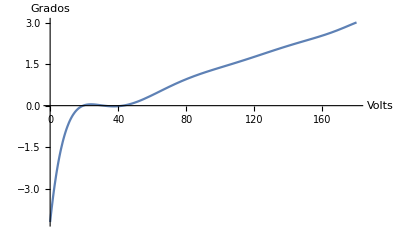

```mathematica
g1=Plot[res,{x,0,180}, AxesLabel-> {"Volts", "Grados"}]
```